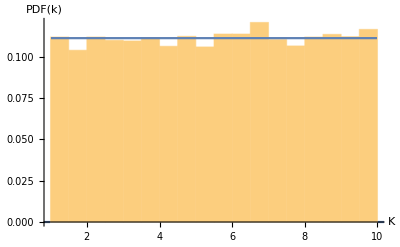
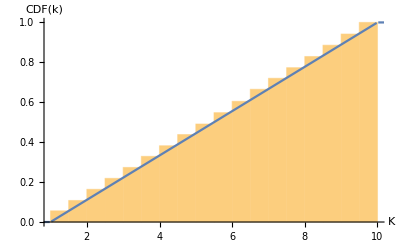
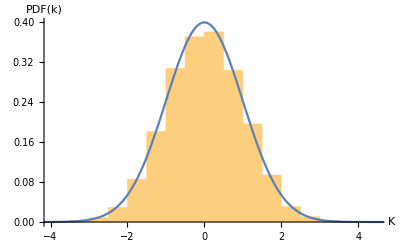
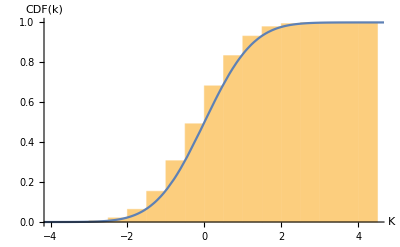
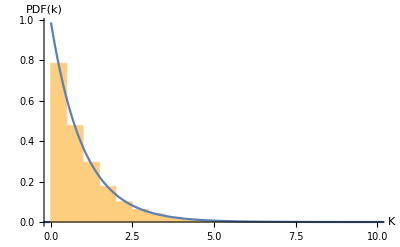
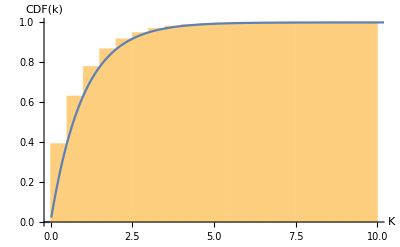
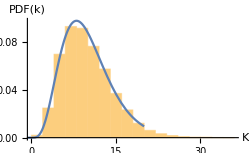
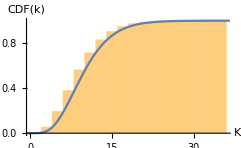
Distribution | PDF | CDF | PDF Histogram | CDF Histogram | Mean | Variance
uniform | Piecewise[{{1/9, 1≤x≤10}, {0, True}}] | Piecewise[{{(x-1)/9, 1≤x≤10}, {1, x>10}}] | -Graphics- | -Graphics- | 5.53663 | 6.75957
normal | (ⅇ^(-x^2/2))/(√(2 π)) | 1/2 erfc(-x/(√2)) | -Graphics- | -Graphics- | 0.0208753 | 0.992338
exponential | Piecewise[{{ⅇ^-x, x≥0}, {0, True}}] | Piecewise[{{1-ⅇ^-x, x≥0}, {0, True}}] | -Graphics- | -Graphics- | 0.997841 | 0.992194
chisquare | Piecewise[{{1/768 ⅇ^(-x/2) x^4, x>0}, {0, True}}] | Piecewise[{{50x/2, x>0}, {0, True}}] | -Graphics- | -Graphics- | 9.93968 | 19.8783
student | 984375/8 (1/(x^2+10))^(11/2) | Piecewise[{{1/2 10/(x^2+10)51/2, x≤0}, {1/2 (x^2/(x^2+10)1/25+1), True}}] | -Graphics- | -Graphics- | -0.0143655 | 1.27537

```mathematica
f[arg_]:=(
str=OpenRead["Visual Studio 2013/Projects/StatMod/"<>arg<>".txt"];
pdf=Read[str, Expression];
cdf=Read[str, Expression];
mean=Read[str, Number];
variance=Read[str, Number];
data=ReadList[str, Number,10000];
Close[str];
{
arg,
pdf//TraditionalForm,
cdf//TraditionalForm,
Show[Histogram[data, 20, "PDF", AxesLabel->{"K","PDF(k)"}], Plot[pdf, {x,-20,20}, PlotRange->Full]],
Show[Histogram[data, 20, "CDF", AxesLabel->{"K","CDF(k)"}], Plot[cdf, {x,-20, 50}]],
mean,
variance
}
)

Grid[Prepend[Table[f[arg], {arg, {"uniform", "normal", "exponential","chisquare", "student"}}],{"Distribution", "PDF","CDF", "PDF Histogram", "CDF Histogram", "Mean", "Variance"}]]
```